x0 = 0. - v0 = 5.

Iteration 1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Violation: -0.5 -- aPoint: 0.375

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

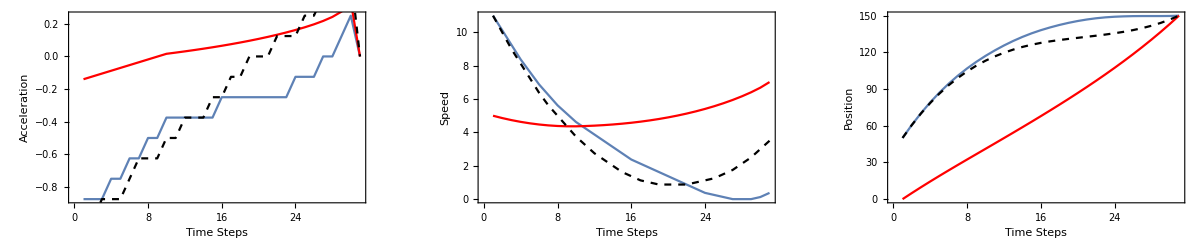

(-0.139709
-0.122392
-0.105075
-0.0877582
-0.0704413
-0.0531243
-0.0358074
-0.0184905
-0.00117352
0.0161434
0.0234439
0.0310673
0.0390361
0.0473743
0.0561362
0.065355
0.0750692
0.0853233
0.0961705
0.107675
0.119925
0.133005
0.147026
0.162148
0.178617
0.196843
0.21761
0.24225
0.275062
0.337679
0.)(0.
4.93015
9.72924
14.4146
19.0035
23.5134
27.9615
32.365
36.7415
41.1081
45.4822
49.8761
54.2973
58.7535
63.2529
67.804
72.4159
77.0981
81.8604
86.7134
91.6684
96.7372
101.932
107.268
112.758
118.418
124.266
130.321
136.606
143.15
150.)(5.
4.86029
4.7379
4.63282
4.54507
4.47462
4.4215
4.38569
4.3672
4.36603
4.38217
4.40562
4.43668
4.47572
4.52309
4.57923
4.64458
4.71965
4.80498
4.90115
5.00882
5.12875
5.26175
5.40878
5.57093
5.74954
5.94639
6.164
6.40625
6.68131
7.01899)

0.42872

Iteration 2

Violation: 0. -- aPoint: 0.337679

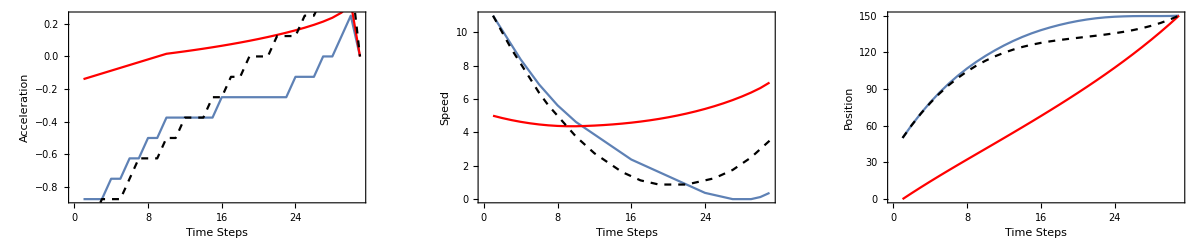

(-0.139054
-0.12179
-0.104527
-0.0872635
-0.0700001
-0.0527367
-0.0354732
-0.0182098
-0.000946401
0.016317
0.0235971
0.0312003
0.0391502
0.0474731
0.0561982
0.065358
0.0749889
0.0851327
0.0958375
0.10716
0.119168
0.131946
0.145605
0.160296
0.17624
0.193798
0.213634
0.237216
0.26883
0.329887
0.)(0.
4.93047
9.73052
14.4174
19.0084
23.5208
27.9718
32.3787
36.7587
41.1292
45.5073
49.9055
54.331
58.7917
63.2957
67.8515
72.4681
77.1549
81.9218
86.7791
91.7379
96.8099
102.007
107.344
112.833
118.491
124.333
130.379
136.651
143.176
150.)(5.
4.86095
4.73916
4.63463
4.54737
4.47737
4.42463
4.38916
4.37095
4.37
4.38632
4.40991
4.44111
4.48026
4.52774
4.58394
4.64929
4.72428
4.80941
4.90525
5.01241
5.13158
5.26353
5.40913
5.56943
5.74567
5.93947
6.1531
6.39032
6.65915
6.98903)

0.0128526

Iteration 3

Violation: 0. -- aPoint: 0.329887

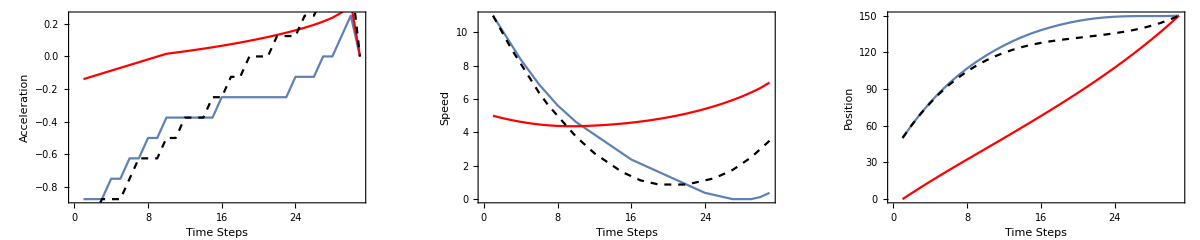

(-0.139053
-0.12179
-0.104526
-0.0872629
-0.0699994
-0.052736
-0.0354726
-0.0182092
-0.000945837
0.0163176
0.0235978
0.0312009
0.0391509
0.0474739
0.056199
0.0653587
0.0749895
0.0851332
0.0958377
0.10716
0.119167
0.131945
0.145603
0.160292
0.176234
0.19379
0.213623
0.237201
0.268811
0.329865
0.)(0.
4.93047
9.73053
14.4174
19.0084
23.5208
27.9718
32.3787
36.7587
41.1292
45.5074
49.9055
54.331
58.7917
63.2957
67.8516
72.4682
77.155
81.9219
86.7792
91.738
96.8101
102.008
107.344
112.833
118.491
124.333
130.38
136.651
143.176
150.)(5.
4.86095
4.73916
4.63463
4.54737
4.47737
4.42463
4.38916
4.37095
4.37
4.38632
4.40992
4.44112
4.48027
4.52775
4.58395
4.6493
4.72429
4.80943
4.90526
5.01242
5.13159
5.26354
5.40914
5.56943
5.74566
5.93946
6.15308
6.39028
6.65909
6.98896)

Terminal criterion met

```mathematica
ClearAll["Global`*"]
dataFolder=StringJoin[NotebookDirectory[],"results_ddp_mathematica"];
SetDirectory[dataFolder];


readScenario[x0_,v0_]:=Module[{x=x0,v=v0},
scenarioFile=StringForm["deterministic x0=`` - v0=``.txt",NumberForm[x,{3,1}],NumberForm[v,{3,1}]];
importFile=StringJoin[NotebookDirectory[],"results_sdp/deterministic/",ToString[scenarioFile]];
scenarioData=Import[importFile,"Table"];
xInit=scenarioData[[All,2]];
vInit=scenarioData[[All,3]];
aInit=scenarioData[[All,4]];
]
Analytical Solution;
t0 =.;te=.;
x0=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.; w=.;

(*ff[xx_,vv_,aa_]:=aa-2*(xxU-xx-vv*TT)/TT^2;
Normal[Series[ff[(xx-xx0) t+xx0,(vv-vv0) t+vv0,(aa-aa0) t+aa0],{t,0,2}]]/.t->1//Print;*)

f[x_]:=0.5*x^2;
lamda1[t_] := c1;
lamda2[t_] := -c1*t-c2;
a[t_] := c1*t+c2;
v[t_] := 0.5*c1*t^2 + c2*t + c3;
x[t_] := N[(1.0/6.0)]*c1*t^3 + 0.5*c2*t^2 + c3*t + c4; 

c = Solve[{v[t0] == v0, v[te] == ve, x[t0] == x0, x[te] == xe}, {c1,c2,c3,c4}];
c1 = c1/.c[[1]];c2 = c2/.c[[1]];c3 = c3/.c[[1]];c4 = c4/.c[[1]];

H[t_] := f[a[t]] +lamda1[t]*v[t] +lamda2[t]*a[t];
theta[t_]:=t*w;
Fte[te_]:=H[te]+D[theta[te],te];
myFitting[xxPoint_,vvPoint_,initTime_]:=(
xPoint=xxPoint;vPoint=vvPoint;
xmin=Max[0,xPoint-epsilonx];xmax=Min[150+epsilonx,xPoint+epsilonx];
vmin=Max[0,vPoint-epsilonv];vmax=Min[16,vPoint+epsilonv];
(*t0=initTime-1;*)
t0=initTime;

A=.;b=.;
stepx=N[(xmax-xmin)/(fitPointsx-1)];stepv=N[(vmax-vmin)/(fitPointsv-1)];
fitx=Table[xmin+(i-1)*stepx,{i,1,fitPointsx}];fitv=Table[vmin+(i-1)*stepv,{i,1,fitPointsv}];
outte=Table[-1.0,{i,fitPointsx},{j,fitPointsv}];outCost=Table[-1.0,{i,fitPointsx},{j,fitPointsv}];
data=Table[-1,{i,1,fitPointsx},{j,1,fitPointsv}];

For[i=1,i≤fitPointsx,i++,
x0=fitx[[i]];
For[j=1,j≤fitPointsv,j++,
v0=fitv[[j]];te=.;
s=FindRoot[Fte[te]==0, {te,t0+0.1}];
tt=te/.s[[1]];outte[[i,j]]=tt]];

For[i=1,i≤fitPointsx,i++,
x0=fitx[[i]];
For[j=1,j≤fitPointsv,j++,
v0=fitv[[j]];
te=outte[[i,j]];outCost[[i,j]]=Integrate[f[a[t]],{t,t0,te}];data[[i,j]]={x0,v0,outCost[[i,j]]}]];

count=1;
lsData=Table[-1,{i,1,fitPointsx*fitPointsv}];
wp=Table[1,{i,1,fitPointsx*fitPointsv}];
weights=Table[1,{i,1,fitPointsx},{i,1,fitPointsv}];
gaussianFunction[x_,v_,spanx_,spanv_]:=Exp[-((x-xPoint)^2/(2spanx^2)+(v-vPoint)^2/(2spanv^2))];
For[i=1,i≤fitPointsx,i++,
For[j=1,j≤fitPointsv,j++,
lsData[[count]]=data[[i,j]];
(*spanx=epsilonx+epsilonv;spanv=epsilonv+epsilonx;*)
(*uij=((lsData[[count,1]]-xPoint)/(spanx)+(lsData[[count,2]]-vPoint)/(spanv));
wp[[count]]=Piecewise[{{(1-Abs[uij]^3)^3, Abs[uij]≤1}, {0, Abs[uij]>1}}];*)
spanx=2*epsilonx^2;spanv=2*epsilonv^2;
wp[[count]]=gaussianFunction[lsData[[count,1]],lsData[[count,2]],spanx,spanv];
weights[[i,j]]=wp[[count]];
count=count+1]];

wp=N[wp];
n=Length[lsData];
dx[i_]:=(lsData[[i,1]]-xPoint);
dv[i_]:=(lsData[[i,2]] -vPoint);
dy[i_]:=(lsData[[i,3]] );

A=({{∑_(i=1)^n (wp[[i]]*dx[i]^4), ∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]^3*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]^3), ∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]^2)}, {∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dv[i]^4), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^3), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dv[i]^3), ∑_(i=1)^n (wp[[i]]*dv[i]^2)}, {∑_(i=1)^n (wp[[i]]*dx[i]^3*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^3), ∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i])}, {∑_(i=1)^n (wp[[i]]*dx[i]^3), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i])}, {∑_(i=1)^n (wp[[i]]*dx[i]^2*dv[i]), ∑_(i=1)^n (wp[[i]]*dv[i]^3), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]), ∑_(i=1)^n (wp[[i]]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dv[i])}, {∑_(i=1)^n (wp[[i]]*dx[i]^2), ∑_(i=1)^n (wp[[i]]*dv[i]^2), ∑_(i=1)^n (wp[[i]]*dx[i]*dv[i]), ∑_(i=1)^n (wp[[i]]*dx[i]), ∑_(i=1)^n (wp[[i]]*dv[i]), ∑_(i=1)^n (wp[[i]]*1)}});

b=({{∑_(i=1)^n (dx[i]^2*dy[i]*wp[[i]])}, {∑_(i=1)^n (dv[i]^2*dy[i]*wp[[i]])}, {∑_(i=1)^n (dx[i]*dv[i]*dy[i]*wp[[i]])}, {∑_(i=1)^n (dx[i]*dy[i]*wp[[i]])}, {∑_(i=1)^n (dv[i]*dy[i]*wp[[i]])}, {∑_(i=1)^n (dy[i]*wp[[i]])}});

lp=LinearSolve[A,b];
p1=lp[[1,1]];p2=lp[[2,1]];p3=lp[[3,1]];p4=lp[[4,1]];p5=lp[[5,1]];p6=lp[[6,1]];
(*StringForm["p1: ``, p2: ``, p3: ``, p4: ``, p5: ``, p6: ``",p1,p2,p3,p4,p5,p6]//Print;*)
(*StringForm["{ ``, ``, ``, ``, ``, `` },",p1,p2,p3,p4,p5,p6]//Print;*)
qPlot[dx_,dv_]:=p1*dx^2+p2*dv^2+p3*dx*dv+p4*dx+p5*dv+p6;

);
Data;
xe=220.0;ve=11.0;w=0.1;t0=31.0;K=31;T=1.0;eps=1.0;pen=1.0;xU=150.0;
iterations=100;epsilon=0.0001;epsilonx=6;epsilonv=3;fitPointsx=5;fitPointsv=5;
prob=Table[0.0,{i,1,K}];
CONSTRAINED=1;STOCHASTIC=1;TERMINALCON=0;

SCENARIO=3;
If[SCENARIO==1,
(* optimal DDDP solution - scenario 1: x0=0 -- v0=5 *)
dddpu={-0.12500,-0.12500,-0.12500,-0.12500,-0.12500,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.12500,0.12500,0.12500,0.12500,0.12500,0.12500,0.12500,0.12500,0.25000,0.25000,0.25000,0.25000,0.25000,0.25000,0.37500,0.00000};
dddpv={5.00000,4.87500,4.75000,4.62500,4.50000,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.37500,4.50000,4.62500,4.75000,4.87500,5.00000,5.12500,5.25000,5.37500,5.62500,5.87500,6.12500,6.37500,6.62500,6.87500,7.25000};
dddpx={0.00000,4.93750,9.75000,14.43750,19.00000,23.43750,27.81250,32.18750,36.56250,40.93750,45.31250,49.68750,54.06250,58.43750,62.81250,67.18750,71.62500,76.18750,80.87500,85.68750,90.62500,95.68750,100.87500,106.18750,111.68750,117.43750,123.43750,129.68750,136.18750,142.93750,150.00000};
(* Initial trajectories obtained from the deterministic GLOSA *)
vInit0={5.0000000000000355,4.811738999540683,4.643294946498108,4.494667840872311,4.365857682663291,4.25686447187105,4.167688208495586,4.098328892536901,4.048786523994992,4.019061102869862,4.009152629161509,4.019061102869934,4.048786523995137,4.098328892537117,4.167688208495876,4.2568644718714115,4.365857682663725,4.4946678408728165,4.643294946498687,4.811738999541333,5.0000000000007585,5.20807794787696,5.435972843169941,5.683684685879699,5.9512134760062345,6.238559213549548,6.5457218985096395,6.872701530886509,7.219498110680156,7.586111637890581,7.972542112517783};
xInit0={0.,4.904218087485628,9.630083648220293,14.197413629620769,18.62602497910384,22.935734644086278,27.146359571984867,31.277716710216378,35.34962300619759,39.38189540734529,43.39435086107624,47.406806314807234,51.439078715955034,55.51098501193643,59.64234215016819,63.85296707806712,68.16267674304994,72.59128809253347,77.1586180739345,81.88448363466978,86.78870172215609,91.89108928381022,97.21146326704894,102.76964061928904,108.58543828794726,114.67867322044042,121.06916236418527,127.77672266659863,134.82117107509723,142.22232453709785,150.00000000001734};
aInit0={-0.19816947416774147,-0.17835252675096372,-0.15853557933418594,-0.13871863191740819,-0.11890168450063043,-0.09908473708385268,-0.07926778966707491,-0.05945084225029715,-0.039633894833519395,-0.019816947416741643,0.0,0.01981694741681389,0.03963389483359164,0.05945084225036942,0.07926778966714718,0.09908473708392493,0.11890168450070268,0.13871863191748043,0.1585355793342582,0.17835252675103594,0.1981694741678137,0.2179864215845915,0.23780336900136925,0.257620316418147,0.27743726383492473,0.2972542112517025,0.31707115866848035,0.3368881060852581,0.35670505350203585,0.3765220009188136,0.39633894833559136};
(* scenario 1: x0=0 -- v0=5 *)
(*xInit0={0,4.875,9.5625,14.125,18.5625,22.875,27.0625,31.125,35.125,39.125,43.125,47.125,51.125,55.125,59.1875,63.375,67.6875,72.125,76.6875,81.375,86.25,91.375,96.75,102.375,108.25,114.375,120.75,127.4375,134.5,141.9375,149.75};
vInit0={5,4.75,4.625,4.5,4.375,4.25,4.125,4,4,4,4,4,4,4,4.125,4.25,4.375,4.5,4.625,4.75,5,5.25,5.5,5.75,6,6.25,6.5,6.875,7.25,7.625,8};
aInit0={-0.25,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,0,0,0,0,0,0,0.125,0.125,0.125,0.125,0.125,0.125,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.375,0.375,0.375,0.375,0};*)
];
If[SCENARIO==2,
(* scenario 2: x0=0 -- v0=11 *)
dddpu={-0.75000,-0.75000,-0.62500,-0.62500,-0.50000,-0.50000,-0.50000,-0.37500,-0.37500,-0.37500,-0.37500,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.12500,-0.12500,-0.12500,-0.12500,-0.12500,0.00000,0.00000,0.00000,0.12500,0.25000,0.25000,0.00000};dddpv={11.00000,10.25000,9.50000,8.87500,8.25000,7.75000,7.25000,6.75000,6.37500,6.00000,5.62500,5.25000,5.00000,4.75000,4.50000,4.25000,4.00000,3.75000,3.50000,3.25000,3.12500,3.00000,2.87500,2.75000,2.62500,2.62500,2.62500,2.62500,2.75000,3.00000,3.25000};
dddpx={0.00000,10.62500,20.50000,29.68750,38.25000,46.25000,53.75000,60.75000,67.31250,73.50000,79.31250,84.75000,89.87500,94.75000,99.37500,103.75000,107.87500,111.75000,115.37500,118.75000,121.93750,125.00000,127.93750,130.75000,133.43750,136.06250,138.68750,141.31250,144.00000,146.87500,150.00000};
(* Initial trajectories obtained from the deterministic GLOSA *)
vInit0={11,10.1558,9.35835,8.60767,7.90374,7.24657,6.63616,6.0725,5.55561,5.08547,4.66209,4.28547,3.95561,3.6725,3.43616,3.24657,3.10374,3.00767,2.95835,2.9558,3,3.09096,3.22868,3.41316,3.64439,3.92239,4.24714,4.61865,5.03691,5.50194,6.01372};
xInit0={0,10.574,20.3272,29.3063,37.5581,45.1294,52.0668,58.4173,64.2274,69.5441,74.4139,78.8838,83.0005,86.8106,90.3611,93.6985,96.8698,99.9216,102.901,105.854,108.828,111.869,115.025,118.342,121.867,125.647,129.728,134.157,138.981,144.246,150};
aInit0={-0.867582,-0.820823,-0.774065,-0.727307,-0.680549,-0.633791,-0.587033,-0.540274,-0.493516,-0.446758,-0.4,-0.353242,-0.306484,-0.259726,-0.212967,-0.166209,-0.119451,-0.0726928,-0.0259347,0.0208235,0.0675817,0.11434,0.161098,0.207856,0.254614,0.301372,0.348131,0.394889,0.441647,0.488405,0.535163};
];
If[SCENARIO==3,
(* scenario 3: x0=50 -- v0=11 *)
dddpu={-0.87500,-0.87500,-0.87500,-0.75000,-0.75000,-0.62500,-0.62500,-0.50000,-0.50000,-0.37500,-0.37500,-0.37500,-0.37500,-0.37500,-0.37500,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.25000,-0.12500,-0.12500,-0.12500,0.00000,0.00000,0.12500,0.25000,0.00000};
dddpv={11.00000,10.12500,9.25000,8.37500,7.62500,6.87500,6.25000,5.62500,5.12500,4.62500,4.25000,3.87500,3.50000,3.12500,2.75000,2.37500,2.12500,1.87500,1.62500,1.37500,1.12500,0.87500,0.62500,0.37500,0.25000,0.12500,0.00000,0.00000,0.00000,0.12500,0.37500};
dddpx={50.00000,60.56250,70.25000,79.06250,87.06250,94.31250,100.87500,106.81250,112.18750,117.06250,121.50000,125.56250,129.25000,132.56250,135.50000,138.06250,140.31250,142.31250,144.06250,145.56250,146.81250,147.81250,148.56250,149.06250,149.37500,149.56250,149.62500,149.62500,149.62500,149.68750,149.93750};
(* Initial trajectories obtained from the deterministic GLOSA *)
xInit0={50.0000,60.5000,70.0000,78.5625,86.2500,93.0625,99.0625,104.3750,109.0625,113.1250,116.6250,119.6250,122.1875,124.3750,126.1875,127.6875,128.9375,130.0000,130.9375,131.8125,132.6875,133.5625,134.5000,135.5625,136.7500,138.1250,139.7500,141.6875,144.0000,146.7500,150.0000};
vInit0={11.0000,10.0000,9.0000,8.1250,7.2500,6.3750,5.6250,5.0000,4.3750,3.7500,3.2500,2.7500,2.3750,2.0000,1.6250,1.3750,1.1250,1.0000,0.8750,0.8750,0.8750,0.8750,1.0000,1.1250,1.2500,1.5000,1.7500,2.1250,2.5000,3.0000,3.5000};
aInit0={-1.0000,-1.0000,-0.8750,-0.8750,-0.8750,-0.7500,-0.6250,-0.6250,-0.6250,-0.5000,-0.5000,-0.3750,-0.3750,-0.3750,-0.2500,-0.2500,-0.1250,-0.1250,0.0000,0.0000,0.0000,0.1250,0.1250,0.1250,0.2500,0.2500,0.3750,0.3750,0.5000,0.5000,0.0000};
];

(*aInit=aInit0;vInit=vInit0;xInit=xInit0;*)
Differential Dynamic Programming;
sX={0.0,10.0,20.0,30.0,40.0,50.0,60.0,70.0,80.0,90.0,100.0};
sV={1.0,2.0,3.0,4.0,5.0,6.0,7.0,8.0,9.0,10.0,11.0};
For[loopi=1,loopi<2,loopi++,
For[loopj=5,loopj<6,loopj++,
(*aInit=aInit0;vInit=vInit0;xInit=xInit0;*)
(*start of scenarios loop*)
xInit={};vInit={};aInit={};
StringForm["x0 = `` - v0 = ``",sX[[loopi]],sV[[loopj]]]//Print;
readScenario[sX[[loopi]],sV[[loopj]]];
(*Print[xInit];*)

it=0;
costFullPrev=1000000;
While[True,
(*eps=1.0;*)
StringForm["Iteration ``",it+1]//Print;
alphaStore=Table[{},{i,1,K}];betaStore=Table[{},{i,1,K}];
PPStore=Table[{},{i,1,K}];QQStore=Table[{},{i,1,K}];constStore=Table[0.0,{i,1,K}];

dx1[dx_,dv_,da_]:=dx+dv+0.5*da*T^2;
dv1[dx_,dv_,da_]:=dv+da*T;

(*k=K*)
xPoint=xInit[[K]];vPoint=vInit[[K]];aPoint=aInit[[K]];
myFitting[xPoint,vPoint,K];
qPlot[dx,dv];
termCond[x_]:=0.5*(xPoint^2-xU)^2+(xPoint-xU)*dx+0.5*dx^2;

If[TERMINALCON==0,
L[dx_,dv_]:=qPlot[dx,dv],
L[dx_,dv_]:=qPlot[dx,dv]+termCond[dx]
];
AA=({{D[L[dx,dv],{dx,2}], D[L[dx,dv],dx,dv]}, {D[L[dx,dv],dv,dx], D[L[dx,dv],{dv,2}]}});
If[TERMINALCON==0,
GG=({{p4}, {p5}}),
GG=({{p4+(xPoint-xU)}, {p5}})
];
const=p6;
PP=AA;QQ=GG;
constStore[[K]]=const;

V[dx_,dv_,PP_,QQ_]:=0.5*({{dx, dv}}).PP.({{dx}, {dv}})+({{dx, dv}}).QQ+const;
alpha={{0},{0}};beta={{0,0},{0,0}};
alphaStore[[K]]={{0},{0}};betaStore[[K]]={{0,0},{0,0}};
PPStore[[K]]=PP;QQStore[[K]]=QQ;


(* k<=K-1 *)
For[k=K-1,k≥1,k--,
(*StringForm["k: ``",k]//Print;*)
xPoint=xInit[[k]];vPoint=vInit[[k]];aPoint=aInit[[k]];
If[k≥11 && STOCHASTIC ==1,prob[[k]]=1.0/((K-k)+1.0);myFitting[xPoint,vPoint,k];qPlot[dx,dv];];
aTaylor[da_]:=aPoint* da+0.5*da^2;
constraint[dx_,dv_,xPoint_,vPoint_]:=-(2.0*(xU-xPoint-vPoint*T-0.5*aPoint)/T^2)+2*dx/T^2+2*dv/T^2;

If[STOCHASTIC==1,
L2[dx_,dv_,da_,PP_,QQ_]:=(1.0-prob[[k]])*(aTaylor[da]
+V[dx1[dx,dv,da],dv1[dx,dv,da],PP,QQ][[1,1]])
+prob[[k]]*qPlot[dx,dv],
L2[dx_,dv_,da_,PP_,QQ_]:=aTaylor[da]+V[dx1[dx,dv,da],dv1[dx,dv,da],PP,QQ][[1,1]];
];
L[dx_,dv_,da_,PP_,QQ_]:=L2[dx,dv,da,PP,QQ];

daCoeff=0.0;da2Coeff=0.0;dvCoeff=0.0;dvdaCoeff=0.0;dv2Coeff=0.0;dxCoeff=0.0;dxdaCoeff=0.0;dxdvCoeff=0.0;dx2Coeff=0.0;
coeffList=CoefficientList[L[dx,dv,da,PP,QQ],{dx,dv,da}];
{{{const,daCoeff,da2Coeff},{dvCoeff,dvdaCoeff,trash},{dv2Coeff,trash,trash}},{{dxCoeff,dxdaCoeff,trash},{dxdvCoeff,trash,trash},{trash,trash,trash}},{{dx2Coeff,trash,trash},{trash,trash,trash},{trash,trash,trash}}}=coeffList;


DD=({{D[L[dx,dv,da,PP,QQ],{dx,2}], D[L[dx,dv,da,PP,QQ],dx,dv]}, {D[L[dx,dv,da,PP,QQ],dx,dv], D[L[dx,dv,da,PP,QQ],{dv,2}]}});EE=({{dxdaCoeff, 0.0}, {dvdaCoeff, 0.0}});
FF=({{D[L[dx,dv,da,PP,QQ],{da,2}], 0}, {0, 1.0}});GG=({{dxCoeff}, {dvCoeff}});HH=({{daCoeff}, {0.0}});constStore[[k]]=const;


(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ Constraints ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
qq=-HH-EE.({{xPoint}, {vPoint}});(* or ({{dx}, {dv}}) dld ({{0.0}, {0.0}}) for constraint problem*)

Ct=({{0.0}, {0.0}});d={{0.0}};
If[constraint[0.0,0.0,xPoint,vPoint]+0.75≥-aPoint && CONSTRAINED==1,
Ct=({{-1.0}, {0.0}});d={{constraint[0.0,0.0,xPoint,vPoint]}};
StringForm["Violation: `` -- aPoint: ``",constraint[0.0,0.0,xPoint,vPoint],aPoint]//Print;
];

(* Quadratic Problem for Active Constraints *)
tempCstar=Transpose[Ct].Inverse[FF].Ct;
If[tempCstar[[1,1]]!=0,tempCstar=Inverse[tempCstar]];

Cstar=tempCstar.Transpose[Ct].Inverse[FF];
Hstar=Inverse[FF].(({{1.0, 0.0}, {0.0, 1.0}})-Ct.Cstar);
pStar=Hstar.qq+Transpose[Cstar].d;
lambdaStar=Cstar.qq-tempCstar.d;

(*Print[pStar];Print[lambdaStar];*)
(* test *)
If[lambdaStar[[1,1]]>0,Ct=({{-1.0}, {0.0}});
d={{constraint[0.0,0.0,xPoint,vPoint]}};
tempCstar=Transpose[Ct].Inverse[FF].Ct;
(*If[tempCstar[[1,1]]!=0,tempCstar=Inverse[tempCstar]];*)
Cstar=Inverse[tempCstar].Transpose[Ct].Inverse[FF];
Hstar=Inverse[FF].(({{1.0, 0.0}, {0.0, 1.0}})-Ct.Cstar)];
(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
P=d;
Jx[dx_,dv_,da_]=D[constraint[dx,dv,xPoint,vPoint],dx];
Jv[dx_,dv_,da_]=D[constraint[dx,dv,xPoint,vPoint],dv];
R=({{Jx[xPoint,vPoint,aPoint], Jv[xPoint,vPoint,aPoint]}});

alpha=-Hstar.HH+Transpose[Cstar].P;
beta=-Hstar.Transpose[EE]+Transpose[Cstar].R;
(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)

PP=DD+Transpose[beta].FF.beta+EE.beta+Transpose[beta].Transpose[EE];
QQ=GG+Transpose[beta].FF.alpha+EE.alpha+Transpose[beta].HH;

alphaStore[[k]]=alpha;betaStore[[k]]=beta;
PPStore[[k]]=PP;QQStore[[k]]=QQ;
];


(* Forward Pass *)
While[True,
aInitNext={};vInitNext={};xInitNext={};
xDDP=xInit[[1]];vDDP=vInit[[1]];
vInitNext=AppendTo[vInitNext,vDDP];
xInitNext=AppendTo[xInitNext,xDDP];
costFull=0.0;

For[k=1,k<K,k++,
dxDDP=(xDDP-xInit[[k]]);dvDDP=(vDDP-vInit[[k]]);
uDDP=aInit[[k]]+eps*(alphaStore[[k]])+betaStore[[k]].({{dxDDP}, {dvDDP}});
xDDP=xDDP+vDDP+0.5*uDDP[[1,1]]*T^2;
vDDP=vDDP+uDDP[[1,1]]*T;

aInitNext=AppendTo[aInitNext,uDDP[[1,1]]];vInitNext=AppendTo[vInitNext,vDDP];xInitNext=AppendTo[xInitNext,xDDP];
costFull=costFull+(1.0-prob[[k]])*0.5*aInitNext[[k]]^2+prob[[k]]*qPlot[(xInitNext[[k]]-xInit[[k]]),(vInitNext[[k]]-vInit[[k]])];

];
Break[];
];

AppendTo[aInitNext,0.0];
s1=Show[ListPlot[dddpu,Joined->True,ImageSize->200,Frame->True,FrameLabel->{"Time Steps","Acceleration"}],ListPlot[aInitNext,PlotStyle->Red,Joined->True],ListPlot[aInit0,PlotStyle->{Black,Dashed},Joined->True]];
s2=Show[ListPlot[dddpv,Joined->True,ImageSize->200,Frame->True,FrameLabel->{"Time Steps","Speed"}],ListPlot[vInitNext,PlotStyle->Red,Joined->True],ListPlot[vInit0,PlotStyle->{Black,Dashed},Joined->True]];
s3=Show[ListPlot[dddpx,Joined->True,ImageSize->200,Frame->True,FrameLabel->{"Time Steps","Position"}],ListPlot[xInitNext,PlotStyle->Red,Joined->True],ListPlot[xInit0,PlotStyle->{Black,Dashed},Joined->True]];
GraphicsGrid[{{s1,s2,s3}}]//Print;

(*print trajectories at each iteration*)
defBlue=ColorData[97,1];defOrange=ColorData[97,2];defGreen=ColorData[97,3];
fontSize=58;steps=Table[i,{i,1,30}];steps2=Table[i,{i,1,31}];
plotItAccel=ListLinePlot[{Transpose[{steps,dddpu[[1;;30]]}],Transpose[{steps,aInitNext[[1;;30]]}],Transpose[{steps,aInit0[[1;;30]]}]},
Filling->None,Joined->True,GridLines->Automatic,PlotRange->{Automatic,Automatic},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Acceleration (m/s/s)",None,None}];
plotItSpeed=ListLinePlot[{Transpose[{steps2,dddpv}],Transpose[{steps2,vInitNext}],Transpose[{steps2,vInit0}]},
Filling->None,Joined->True,GridLines->Automatic,PlotRange->{Automatic,Automatic},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Speed (m/s)",None,None}];
plotItPos=ListLinePlot[{Transpose[{steps2,dddpx}],Transpose[{steps2,xInitNext}],Transpose[{steps2,xInit0}]},
Filling->None,Joined->True,GridLines->Automatic,PlotRange->{Automatic,Automatic},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red}},AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Position (m)",None,None}];

Print[MatrixForm[aInitNext],MatrixForm[xInitNext],MatrixForm[vInitNext]];
If[(Norm[aInitNext-aInit]< epsilon || it>=iterations),
Print["Terminal criterion met"];
(*Print[MatrixForm[aInitNext],MatrixForm[xInitNext],MatrixForm[vInitNext]];*)
Break[]
];
Print[Norm[aInitNext-aInit]];

aInit=aInitNext;vInit=vInitNext;xInit=xInitNext;
costFullPrev=costFull;
it=it+1;
];
(*  *)
(*test=StringForm["(``) x0=`` - v0=``.txt",it,NumberForm[xInit[[1]],{3,1}],NumberForm[vInit[[1]],{3,1}]];*)
test=StringForm["x0=`` - v0=``.txt",NumberForm[xInit[[1]],{3,1}],NumberForm[vInit[[1]],{3,1}]];
fname=FileNameJoin[{Directory[],ToString[test]}];
s=OpenWrite[fname];
output=Table[{xInit[[i]],vInit[[i]],aInit[[i]]},{i,1,K}];
Export[s,output, "Table"];
Close[s]
(*end of scenarios loop*)
]
]
```